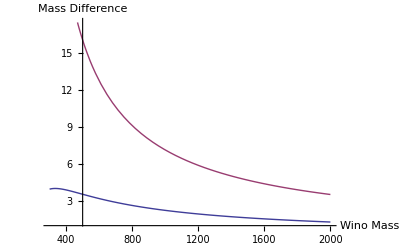

```mathematica
(*
mChi10[μ_,mZ_,M1_,M2_,β_,θW_] :=Abs[μ]+mZ*mZ*(Sign[μ]+Sin[2β])*(μ-M1*Cos[θW]^2-M2*Sin[θW]^2)/(2*(μ-M1)*(μ-M2))
mChi20[μ_,mZ_,M1_,M2_,β_,θW_] :=Abs[μ]+mZ*mZ*(Sign[μ]-Sin[2β])*(μ+M1*Cos[θW]^2+M2*Sin[θW]^2)/(2*(μ+M1)*(μ+M2))

mChi1pm[μ_,mW_,M2_,β_] :=Abs[μ]+mW*mW*Sign[μ]*(μ+M2*Sin[2β])/(μ*μ-M2*M2)
*)

M[μ_,M1_,M2_,mZ_,β_,θW_]:= 
{{M1,0,-Cos[β]Sin[θW]mZ,Sin[β]Sin[θW]mZ},
{0,M2,Cos[β]Cos[θW]mZ,-Sin[β]Cos[θW]mZ},
{-Cos[β]Sin[θW]mZ,Cos[β]Cos[θW]mZ,0,-μ},
{Sin[β]Sin[θW]mZ,-Sin[β]Cos[θW]mZ,-μ,0}}

mChi10[μ_,M1_,M2_,mZ_,β_,θW_]  := Abs[Eigenvalues[M[μ,M1,M2,mZ,β,θW]][[4]]]
mChi20[μ_,M1_,M2_,mZ_,β_,θW_]  := Abs[Eigenvalues[M[μ,M1,M2,mZ,β,θW]][[3]]]


mChi1pm[μ_,mW_,M2_,β_] :=Sqrt[(1/2)*(M2*M2+μ*μ+2mW*mW-Sqrt[(M2*M2+μ*μ+2mW*mW)^2 - 4*(μ*M2-mW*mW*Sin[2β])*(μ*M2-mW*mW*Sin[2β])])]


Plot[{mChi1pm[200,80.4,M2,ArcTan[10]]-mChi10[200,9000,M2,91.2,ArcTan[10],ArcCos[80.4/91.2]] ,mChi20[200,9000,M2,91.2,ArcTan[10],ArcCos[80.4/91.2]]-mChi10[200,9000,M2,91.2,ArcTan[10],ArcCos[80.4/91.2]] },{M2,300,2000},AxesLabel->{"Wino Mass","Mass Difference"}]
```